#### params

```mathematica
Δ=0.005;
σ=0.01;
α=0.001;
ϕ=0.001;
γ=10;
κ=50;
ε=0.005;
Υ=Δ+ε;
χ=0.02;
tiltλ=50/300;
λ=tiltλ*ⅇ^(-κ*Δ);


Ν=10;(*Total Amt*)
T=300;(*Total Time*)
```

```mathematica
(*Market Impact Cost*)
c[q_]:=α*q;
```

```mathematica
(*Target Schedule*)
IS[t_]:=Ν*(1-Sinh[χ*(T-t)]/Sinh[χ*T])
```

#### eqs

```mathematica
ω[t_,q_]:=ⅇ^(-κ*(Υ+c[Ν-q])*(Ν-q))/;t==T
ω[t_,q_]:=Exp[-κ*ϕ*NIntegrate[(Ν-IS[u])^2,{u,t,T}]]/;q==Ν
```

尝试解析解 建议告辞

```mathematica
eqs=(D[ω[t,q],t]-κ*ϕ*(q-IS[t])^2 ω[t,q]+ⅇ^-1 λ ω[t,q+1])*(ω[t,q]-ⅇ^(-κ*Υ)ω[t,q+1])==0
```

(ω[t,q]-0.606531 ω[t,1+q]) (-0.05 (q-10 (1-0.00495753 Sinh[0.02 (300-t)]))^2 ω[t,q]+0.122626 ω[t,1+q]+ω^(1,0)[t,q])==0

数值解尝试
Do it backwards

```mathematica
fdmSolver[t_,dt_,q_]:=
Module[
{time=Subdivide[0,t,Floor[t/dt]],
inventory=Range[0,q,1],
mat
},
mat=ConstantArray[0,{q+1,Length[time]}];
mat[[-1]]=Table[ω[i,q],{i,time}];
(*from t+dt to t*)
Table[
mat[[1;;-2,idxT]]=mat[[1;;-2,idxT+1]]-κ*ϕ*dt*Thread[Times[Power[Range[0,q-1]-IS[time[[idxT+1]]],2],mat[[1;;-2,idxT+1]]]]+ⅇ^-1*λ*dt*mat[[2;;-1,idxT+1]];
mat[[1;;-2,idxT]]=MapThread[Max,{ⅇ^(-κ*Υ)*mat[[2;;-1,idxT]],mat[[1;;-2,idxT]]}];,
{idxT,Range[Length[time]-1,1,-1]}];
mat
]
```

```mathematica
mat=fdmSolver[T,0.1,Ν];
```

```mathematica
RepeatedTiming[fdmSolver[T,0.1,Ν];]
```

{16.4233,Null}

```mathematica
mat[[-1]]==Table[ω[i,10],{i,Subdivide[0,T,Floor[T/0.1]]}]
```

True

```mathematica
ListPlot3D[mat]
```

-Graphics3D-

```mathematica
mat2=fdmSolver[T,0.1,Ν];
```

```mathematica
ListPlot3D[mat2]
```

-Graphics3D-

```mathematica
MapThread[Max,{{2,3,-2},{3,4,2}}]
```

{3,4,2}

#### Price Dynamics

```mathematica
S0=100
```

100

```mathematica
𝒫=TransformedProcess[S0+σ*(up[t]-down[t]),{up\[Distributed]PoissonProcess[γ],down\[Distributed]PoissonProcess[γ]},t];
```

```mathematica
data = RandomFunction[𝒫,{0,T,1},10]
```

TemporalData[…]

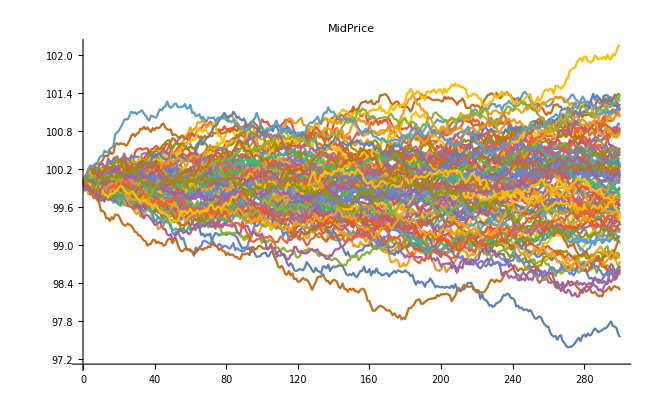

```mathematica
ListLinePlot[ RandomFunction[𝒫,{0,T,1},100],PlotLabel->"MidPrice"]
```